(1 | 3
0 | 4)

x^2+y (3 x+4 y)==5

Solve::svars: Equations may not give solutions for all "solve" variables.

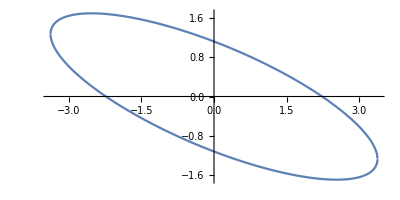

```mathematica
QForm={{1,3},{0,4}};
QForm//MatrixForm
Surf={x,y}.QForm.{x,y}==5
sol=Solve[Surf,{x,y},Reals];
ParametricPlot[{x,y}/.sol,{x,-4,4}]
```